```mathematica
Get[NotebookDirectory[]<>#]&/@
{"combine_packages.wls",
"load_Kramer_data.wl"
};
```

```mathematica
figureNumberFinalStatesBeforeDamageShort="Fig_6";
figureNumberFinalStatesBeforeDamageLong=figureNumberFinalStatesBeforeDamageShort<>"_steady_states_before_damage";
```

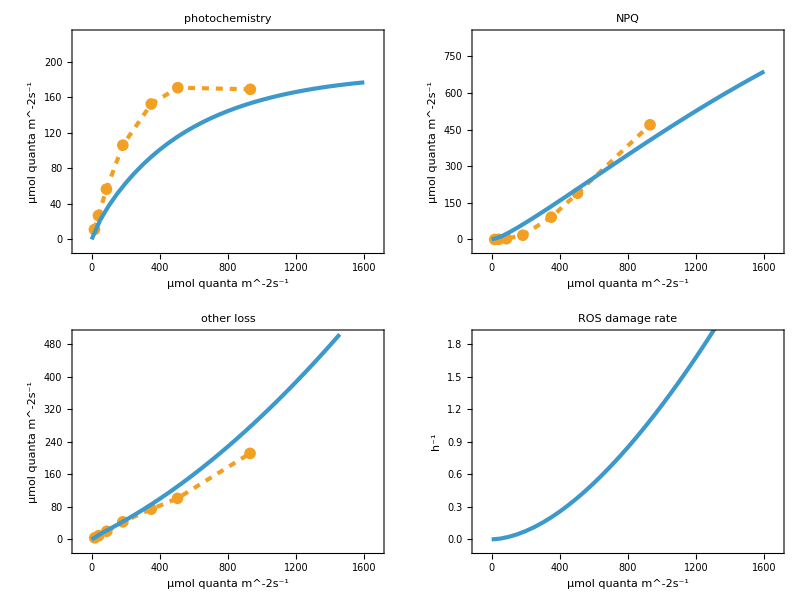

```mathematica
LrangeFates=Range[0,1600,50];
LFateRanges={gP->220,gN->800,gU->480,xD->3600  5 10^-4};
KramerDataPlots=Table[ListPlot[
x/.{gP->gKramer[[1]],gN->gKramer[[2]],gU->gKramer[[3]],xD->{{}}},
PlotRange->{{-.05(Max[LrangeFates]-Min[LrangeFates]),1.05Max[LrangeFates]},{-.05,1.05}(x/.LFateRanges)},PlotLabel->(x/.namesVerbal),imageSizePadding[ImagePaddingUnits],
PlotStyle->{thickness, Dashed,colorPoints},
AxesOrigin->Automatic,
PlotMarkers->plotMarkers,
FrameLabel->{{If[TrueQ[x==xD],"h^-1",L/.units],None},{L/.units,None}},Joined->True,PlotStyle->{AbsoluteThickness[3],Dashed},Evaluate@style],{x,{gP,gN,gU,xD}}];
finalTimeFatePlot=1/60 3600;
LightFateSimulations=Table[makeOneSimulationSteadyStatePlot[pars[0](*Join[parsNoDamage,pars[-6]]*),L,LrangeFates,x, finalTimeFatePlot,{PlotRange->{{-.05(Max[LrangeFates]-Min[LrangeFates]),1.05Max[LrangeFates]},{-.05,1.05}(x/.LFateRanges)},PlotStyle->{{thickness, colorCurves}}}],{x,{gP,gN,gU,3600 xD}}];

(Export[NotebookDirectory[]<>figureNumberFinalStatesBeforeDamageLong<>"/"<>figureNumberFinalStatesBeforeDamageShort<>".pdf",#];#)&@Multicolumn[Table[Show[{KramerDataPlots[[i]],LightFateSimulations[[i]]}],{i,4}], Appearance -> "Horizontal"]
```

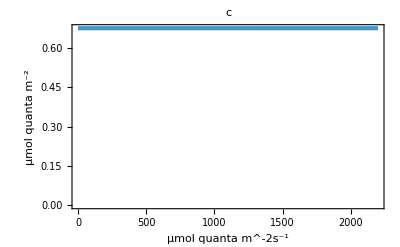
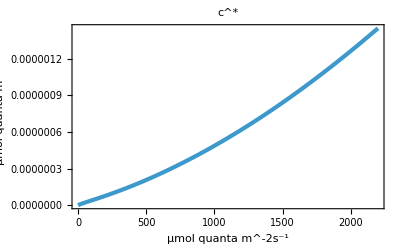
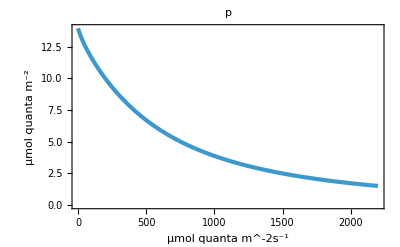
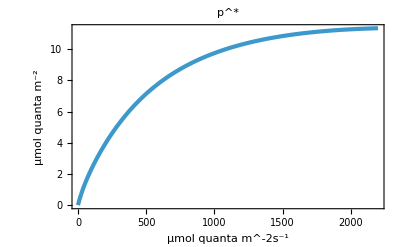
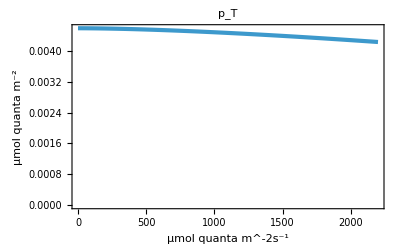
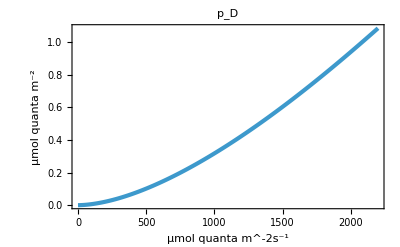
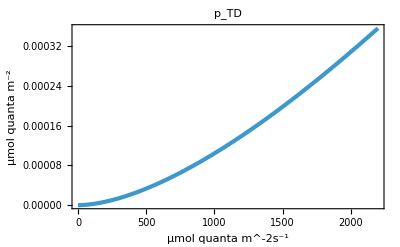
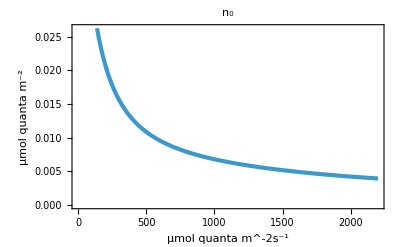

```mathematica
(Export[NotebookDirectory[]<>figureNumberFinalStatesBeforeDamageLong<>"/"<>figureNumberFinalStatesBeforeDamageShort<>"_SI.pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[0],L,Lrange,#,finalTimeFatePlot,{PlotLabel->#/.names}]&,quants]
```